```mathematica
Clear["Global`*"]
```

## Switching model: once infected with good can exchange for better

## Invasion analysis

Fecundity function is b:=F_i b_max Exp[-c pi[x]]

Mutant fecundity matrix Fm - all classes express the resistance π_G1^m when it comes to fecundity.

```mathematica
Fm=(1-κ 𝒩){{bm[S],0,0,0},{0,bm[G1],0,0},{0,0,bm[G2],0},{0,0,0,bm[G1G2]}}/.bm[x_]->F[x]bmax Exp[-c (pi[G1]+pi[G2])]
```

{{bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[S],0,0,0},{0,bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G1],0,0},{0,0,bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G2],0},{0,0,0,bmax ⅇ^(-c (pi[G1]+pi[G2])) (1-𝒩 κ) F[G1G2]}}

```mathematica
D[bmax Exp[-c (pi[G1]+pi[G2])]F[x],pi[G1]]
```

-bmax c ⅇ^(-c (pi[G1]+pi[G2])) F[x]

```mathematica
Vm=-{{-(d+ψ[G1]+ψ[G2]),γ[G1],γ[G2],0},
{ψ[G1],-(d[G1]+γ[G1]+λ(1-σ)(1-pi[G2])ψ[G2]+σ(1-pi[G2])ψ[G2]),λ(1-σ)(1-pi[G1])ψ[G1],γ[G2]},
{ψ[G2],λ(1-σ)(1-pi[G2])ψ[G2],-(d[G2]+γ[G2]+λ(1-σ)(1-pi[G1])ψ[G1]+σ(1-pi[G1])ψ[G1]),γ[G1]},
{0,σ(1-pi[G2])ψ[G2],σ(1-pi[G1])ψ[G1],-(d[G1G2]+γ[G1]+γ[G2])}
}
```

{{d+ψ[G1]+ψ[G2],-γ[G1],-γ[G2],0},{-ψ[G1],d[G1]+γ[G1]+λ (1-σ) (1-pi[G2]) ψ[G2]+σ (1-pi[G2]) ψ[G2],-λ (1-σ) (1-pi[G1]) ψ[G1],-γ[G2]},{-ψ[G2],-λ (1-σ) (1-pi[G2]) ψ[G2],d[G2]+γ[G2]+λ (1-σ) (1-pi[G1]) ψ[G1]+σ (1-pi[G1]) ψ[G1],-γ[G1]},{0,-σ (1-pi[G2]) ψ[G2],-σ (1-pi[G1]) ψ[G1],d[G1G2]+γ[G1]+γ[G2]}}

```mathematica
-Vm//MatrixForm
```

(-d-ψ[G1]-ψ[G2] | γ[G1] | γ[G2] | 0
ψ[G1] | -d[G1]-γ[G1]-λ (1-σ) (1-pi[G2]) ψ[G2]-σ (1-pi[G2]) ψ[G2] | λ (1-σ) (1-pi[G1]) ψ[G1] | γ[G2]
ψ[G2] | λ (1-σ) (1-pi[G2]) ψ[G2] | -d[G2]-γ[G2]-λ (1-σ) (1-pi[G1]) ψ[G1]-σ (1-pi[G1]) ψ[G1] | γ[G1]
0 | σ (1-pi[G2]) ψ[G2] | σ (1-pi[G1]) ψ[G1] | -d[G1G2]-γ[G1]-γ[G2])

```mathematica
Bm=Fm -Vm;
```

```mathematica
Bm/.pi[G2]->0/.λ->1//Simplify//MatrixForm
```

(-d+bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[S]-ψ[G1]-ψ[G2] | γ[G1] | γ[G2] | 0
ψ[G1] | -d[G1]+ⅇ^(-c pi[G1]) (bmax-bmax 𝒩 κ) F[G1]-γ[G1]-ψ[G2] | (-1+σ) (-1+pi[G1]) ψ[G1] | γ[G2]
ψ[G2] | -(-1+σ) ψ[G2] | -d[G2]+ⅇ^(-c pi[G1]) (bmax-bmax 𝒩 κ) F[G2]-γ[G2]-ψ[G1]+pi[G1] ψ[G1] | γ[G1]
0 | σ ψ[G2] | -σ (-1+pi[G1]) ψ[G1] | -d[G1G2]+ⅇ^(-c pi[G1]) (bmax-bmax 𝒩 κ) F[G1G2]-γ[G1]-γ[G2])

```mathematica
D[Bm,pi[G1]]/.{pi[G2]->0,λ->1}//MatrixForm
```

(-bmax c ⅇ^(-c pi[G1]) (1-𝒩 κ) F[S] | 0 | 0 | 0
0 | -bmax c ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G1] | -(1-σ) ψ[G1] | 0
0 | 0 | -bmax c ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G2]+(1-σ) ψ[G1]+σ ψ[G1] | 0
0 | 0 | -σ ψ[G1] | -bmax c ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G1G2])

```mathematica
dynamic=Bm.Transpose[{{𝒮,IG1,IG2,IG1G2}}]/.{pi[G2]->0,λ->1}
```

{{IG1 γ[G1]+IG2 γ[G2]+𝒮 (-d+bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[S]-ψ[G1]-ψ[G2])},{IG1G2 γ[G2]+𝒮 ψ[G1]+IG2 (1-σ) (1-pi[G1]) ψ[G1]+IG1 (-d[G1]+bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G1]-γ[G1]-(1-σ) ψ[G2]-σ ψ[G2])},{IG1G2 γ[G1]+IG2 (-d[G2]+bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G2]-γ[G2]-(1-σ) (1-pi[G1]) ψ[G1]-σ (1-pi[G1]) ψ[G1])+𝒮 ψ[G2]+IG1 (1-σ) ψ[G2]},{IG1G2 (-d[G1G2]+bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G1G2]-γ[G1]-γ[G2])+IG2 σ (1-pi[G1]) ψ[G1]+IG1 σ ψ[G2]}}

```mathematica
dynamic[[4]]
```

{IG1G2 (-d[G1G2]+bmax ⅇ^(-c pi[G1]) (1-𝒩 κ) F[G1G2]-γ[G1]-γ[G2])+IG2 σ (1-pi[G1]) ψ[G1]+IG1 σ ψ[G2]}

```mathematica
u
```

u

```mathematica
BmNG=Fm.Inverse[Vm];
```

```mathematica
evalsBmNGCase1=BmNG[[1;;3,1;;3]]/.{γ[G1]->0,γ[G2]->0,F[S]->0,κ->0,F[G1G2]->0,σ->0}//Eigenvalues;
```

```mathematica
evalsBmNGCase1Simpl=evalsBmNGCase1/.{pi[G2]->0,F[G2]->F[G1]+δ,γ[G1]->0,γ[G2]->0,ψ[G1]->ψ,ψ[G2]->ψ,d[G1]->dx,d[G2]->d,F[S]->0}//Simplify
```

{0,1/(2 (dx λ ψ+d (dx+λ ψ)-dx λ ψ pi[G1]))bmax ⅇ^(-c pi[G1]) (dx δ+δ λ ψ+F[G1] (d+dx+2 λ ψ-λ ψ pi[G1])+√(δ^2 (dx+λ ψ)^2-2 δ F[G1] (d dx-dx^2+d λ ψ-dx λ ψ-2 λ^2 ψ^2+λ ψ (-dx+λ ψ) pi[G1])+F[G1]^2 (d^2-2 d dx+dx^2+4 λ^2 ψ^2-2 λ ψ (d-dx+2 λ ψ) pi[G1]+λ^2 ψ^2 pi[G1]^2))),1/(2 (dx λ ψ+d (dx+λ ψ)-dx λ ψ pi[G1]))bmax ⅇ^(-c pi[G1]) (dx δ+δ λ ψ+F[G1] (d+dx+2 λ ψ-λ ψ pi[G1])-√(δ^2 (dx+λ ψ)^2-2 δ F[G1] (d dx-dx^2+d λ ψ-dx λ ψ-2 λ^2 ψ^2+λ ψ (-dx+λ ψ) pi[G1])+F[G1]^2 (d^2-2 d dx+dx^2+4 λ^2 ψ^2-2 λ ψ (d-dx+2 λ ψ) pi[G1]+λ^2 ψ^2 pi[G1]^2)))}

```mathematica
ΔpiG1=D[evalsBmNGCase1Simpl,pi[G1]]/.{pi[G2]->0,pi[G1]->0};
```

```mathematica
ΔpiG1[[3]]//Simplify
```

1/(2 (dx λ ψ+d (dx+λ ψ))^2)bmax (λ ψ (dx λ ψ+d (dx+λ ψ)) F[G1] (-1+(-dx δ+δ λ ψ+(d-dx+2 λ ψ) F[G1])/(√(δ^2 (dx+λ ψ)^2+2 δ (dx^2+dx λ ψ+2 λ^2 ψ^2-d (dx+λ ψ)) F[G1]+(d^2-2 d dx+dx^2+4 λ^2 ψ^2) F[G1]^2)))+dx λ ψ (dx δ+δ λ ψ+(d+dx+2 λ ψ) F[G1]-√(δ^2 (dx+λ ψ)^2+2 δ (dx^2+dx λ ψ+2 λ^2 ψ^2-d (dx+λ ψ)) F[G1]+(d^2-2 d dx+dx^2+4 λ^2 ψ^2) F[G1]^2))-c (dx λ ψ+d (dx+λ ψ)) (dx δ+δ λ ψ+(d+dx+2 λ ψ) F[G1]-√(δ^2 (dx+λ ψ)^2+2 δ (dx^2+dx λ ψ+2 λ^2 ψ^2-d (dx+λ ψ)) F[G1]+(d^2-2 d dx+dx^2+4 λ^2 ψ^2) F[G1]^2)))

```mathematica
ΔpiG1[[3]]/.{λ->1,pi[G2]->0,pi[G1]->0,σ->0}/.{bmax->1,c->0.1,F[G1]->1}
```

(-ψ-(-2 δ ψ (-dx+ψ)-2 ψ (d-dx+2 ψ))/(2 √(d^2-2 d dx+dx^2+4 ψ^2+δ^2 (dx+ψ)^2-2 δ (d dx-dx^2+d ψ-dx ψ-2 ψ^2))))/(2 (dx ψ+d (dx+ψ)))+(dx ψ (d+dx+dx δ+2 ψ+δ ψ-√(d^2-2 d dx+dx^2+4 ψ^2+δ^2 (dx+ψ)^2-2 δ (d dx-dx^2+d ψ-dx ψ-2 ψ^2))))/(2 (dx ψ+d (dx+ψ))^2)-(0.05 (d+dx+dx δ+2 ψ+δ ψ-√(d^2-2 d dx+dx^2+4 ψ^2+δ^2 (dx+ψ)^2-2 δ (d dx-dx^2+d ψ-dx ψ-2 ψ^2))))/(dx ψ+d (dx+ψ))

```mathematica
Plot3D[evalsBmNGCase1Simpl[[3]]/.{λ->1,pi[G2]->0,pi[G1]->0}/.{bmax->1,c->0.1,F[G1]->1,d->50,dx->50},{δ,0,20},{ψ,0,10}]
```

-Graphics3D-

```mathematica
plotTx=Table[Plot3D[evalsBmNGCase1Simpl[[2]]/.{pi[G1]->0,λ->1,bmax->50,c->cx,F[G1]->5,d->1,dx->2},{δ,0,20},{ψ,0,10},PlotRange->{0,Automatic}],{cx,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
plotT=Table[Plot3D[Max[evalsBmNGCase1Simpl]/.{pi[G1]->0,λ->1,bmax->50,c->cx,F[G1]->5,d->1,dx->2},{δ,0,20},{ψ,0,10},PlotRange->{0,Automatic}],{cx,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ΔpiNonZero=D[evalsBmNGCase1Simpl,pi[G1]]/.{pi[G2]->0};
```

```mathematica
Plot3D[ΔpiNonZero[[2]]/.{λ->1,bmax->50,c->0.1,F[G1]->1,d->1,ψ->5,dx->10},{δ,0,20},{pi[G1],0,1}]
```

-Graphics3D-

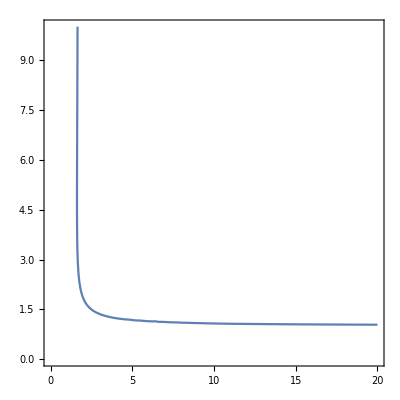
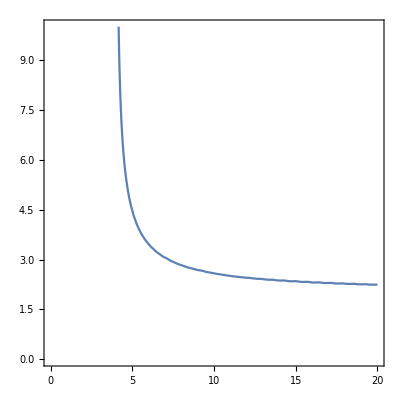
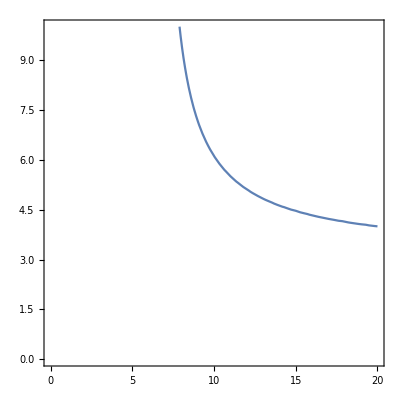

```mathematica
plotT=Table[ContourPlot[(ΔpiG1[[2]]/.{λ->1,bmax->50,c->cx,F[G1]->1,d->1,dx->2})==0,{δ,0,20},{ψ,0,10}],{cx,{0.4,0.5,0.55}}]
```

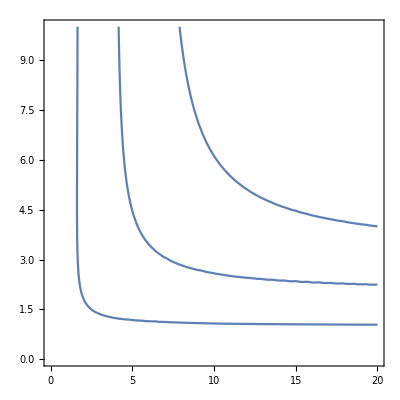

```mathematica
Show[plotT]
```

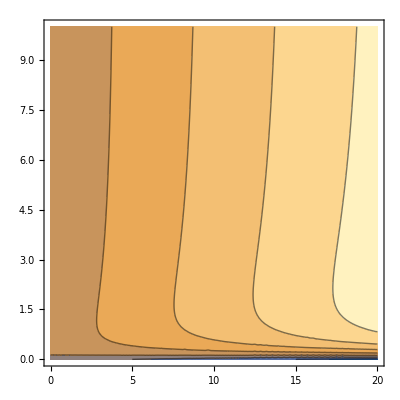
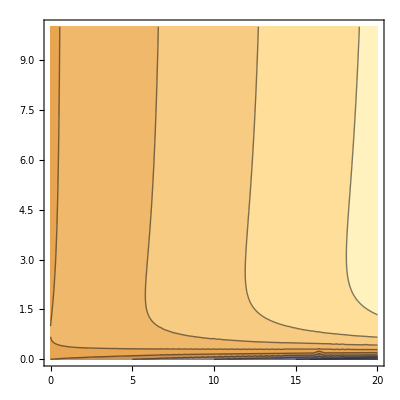

```mathematica
plotT=Table[ContourPlot[(ΔpiG1[[2]]/.{λ->1,bmax->50,c->cx,F[G1]->5,d->1,dx->2}),{δ,0,20},{ψ,0,10}],{cx,{0.1,0.2}}]
```

```mathematica
(δ^2 (d+ψ)^2+4 δ ψ^2 F[G1]+4 ψ^2 F[G1]^2/.δ->0)+δ( D[δ^2 (d+ψ)^2+4 δ ψ^2 F[G1]+4 ψ^2 F[G1]^2,δ]/.δ->0)//Simplify
```

4 ψ^2 F[G1] (δ+F[G1])

```mathematica
(bmax (ψ (d+2 ψ) F[G1] (-1+(δ (d-ψ)-2 ψ F[G1])/u)+ψ (d δ+δ ψ+2 (d+ψ) F[G1]+u)-c (d+2 ψ) (d δ+δ ψ+2 (d+ψ) F[G1]+u)))/(2 d (d+2 ψ)^2)//Simplify
```

(bmax (-(ψ (d+2 ψ) F[G1] (u+δ (-d+ψ)+2 ψ F[G1]))/u+ψ (u+δ (d+ψ)+2 (d+ψ) F[G1])-c (d+2 ψ) (u+δ (d+ψ)+2 (d+ψ) F[G1])))/(2 d (d+2 ψ)^2)

```mathematica
ans1=-ψ (d+2 ψ) F[G1] (u+δ (-d+ψ)+2 ψ F[G1])-u(c (d+2 ψ) (u+δ (d+ψ)+2 (d+ψ) F[G1]))+u(ψ (u+δ (d+ψ)+2 (d+ψ) F[G1]))
```

-ψ (d+2 ψ) F[G1] (u+δ (-d+ψ)+2 ψ F[G1])+u ψ (u+δ (d+ψ)+2 (d+ψ) F[G1])-c u (d+2 ψ) (u+δ (d+ψ)+2 (d+ψ) F[G1])

```mathematica
(ans1/.δ->0)//FullSimplify
```

-ψ (d+2 ψ) F[G1] (u+2 ψ F[G1])+u ψ (u+2 (d+ψ) F[G1])-c u (d+2 ψ) (u+2 (d+ψ) F[G1])

```mathematica
(D[ans1,δ]/.δ->0)
```

u ψ (d+ψ)-c u (d+ψ) (d+2 ψ)-ψ (-d+ψ) (d+2 ψ) F[G1]

Attractor very similar to Gandon & Vale obvz, but important difference, 1st eigenvalue unlikely to be dominant, hence selection against resistance of any of the types...

```mathematica
Solve[((-1+c-c pi[G1]) ψ[G1]+c (d+ψ[G2]))==0,pi[G1]]//Simplify
```

{{pi[G1]→(-1+c)/c+(d+ψ[G2])/ψ[G1]}}

```mathematica
D[evalsBmNGCase1,pi[G1],pi[G1]]/.{pi[G1]->0,pi[G2]->0}//Simplify
```

{(bmax F[S] ((2-2 c+c^2) ψ[G1]^2+2 (-1+c) c ψ[G1] (d+ψ[G2])+c^2 (d+ψ[G2])^2))/(d+ψ[G1]+ψ[G2])^3,(bmax c^2 F[G1])/d[G1],(bmax c^2 F[G2])/d[G2]}

```mathematica
BmCase1=Bm[[1;;3,1;;3]]/.{σ->0,pi[G2]->0,κ->0}//Simplify
```

{{-d+bmax ⅇ^(-c pi[G1]) F[S]+(-1+pi[G1]) ψ[G1]-ψ[G2],γ[G1],γ[G2]},{-(-1+pi[G1]) ψ[G1],-d[G1]+bmax ⅇ^(-c pi[G1]) F[G1]-γ[G1],0},{ψ[G2],0,-d[G2]+bmax ⅇ^(-c pi[G1]) F[G2]-γ[G2]}}

```mathematica
BmCase1//MatrixForm
```

(-d+bmax ⅇ^(-c pi[G1]) F[S]+(-1+pi[G1]) ψ[G1]-ψ[G2] | γ[G1] | γ[G2]
-(-1+pi[G1]) ψ[G1] | -d[G1]+bmax ⅇ^(-c pi[G1]) F[G1]-γ[G1] | 0
ψ[G2] | 0 | -d[G2]+bmax ⅇ^(-c pi[G1]) F[G2]-γ[G2])

```mathematica
BmCase1MainResult=BmCase1/.{γ[G1]->0,γ[G2]->0}//Eigenvalues//Simplify
```

{-d[G1]+bmax ⅇ^(-c pi[G1]) F[G1],-d[G2]+bmax ⅇ^(-c pi[G1]) F[G2],-d+bmax ⅇ^(-c pi[G1]) F[S]+(-1+pi[G1]) ψ[G1]-ψ[G2]}

```mathematica
BmCase1MainResult/.{F[S]->0,pi[G1]->0}//Simplify
```

{-d[G1]+bmax F[G1],-d[G2]+bmax F[G2],-d-ψ[G1]-ψ[G2]}

```mathematica
D[BmCase1MainResult,pi[G1]]/.{pi[G1]->0,F[S]->0}//Simplify
```

{-bmax c F[G1],-bmax c F[G2],ψ[G1]}

```mathematica
evalx=BmCase1//Eigenvalues;
```

```mathematica
selgrad=D[evalx,pi[G1]]/.{pi[G1]->0,F[G2]->F[G1]+δ,γ[G1]->0,γ[G2]->0,ψ[G1]->ψ,ψ[G2]->ψ,d[G1]->d,d[G2]->d,F[S]->0}//Simplify;
```

```mathematica
selgrad[[1]]//Variables
```

{bmax,c,d,δ,ψ,F[G1]}

```mathematica
selgrad[[1]]
```

-c Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]-(3 c d^3-d^2 ψ+6 c d^2 ψ-2 bmax c d^2 F[G1]+bmax d ψ F[G1]-4 bmax c d ψ F[G1]-2 bmax c d^2 (δ+F[G1])+bmax d ψ (δ+F[G1])-4 bmax c d ψ (δ+F[G1])+bmax^2 c d F[G1] (δ+F[G1])-bmax^2 ψ F[G1] (δ+F[G1])+2 bmax^2 c ψ F[G1] (δ+F[G1])+(-2 d ψ+bmax δ ψ+c (6 d^2-2 bmax d δ+8 d ψ-2 bmax δ ψ)+2 bmax (ψ-2 c (d+ψ)) F[G1]) Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]+(3 c d-ψ+2 c ψ) Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]^2)/(3 d^2+4 d ψ-2 bmax d F[G1]-2 bmax ψ F[G1]-2 bmax d (δ+F[G1])-2 bmax ψ (δ+F[G1])+bmax^2 F[G1] (δ+F[G1])+2 (3 d-bmax δ+2 ψ-2 bmax F[G1]) Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]+3 Root[d^3-bmax d^2 δ+2 d^2 ψ-2 bmax d δ ψ-2 bmax d^2 F[G1]+bmax^2 d δ F[G1]-4 bmax d ψ F[G1]+2 bmax^2 δ ψ F[G1]+bmax^2 d F[G1]^2+2 bmax^2 ψ F[G1]^2+(3 d^2-2 bmax d δ+4 d ψ-2 bmax δ ψ-4 bmax d F[G1]+bmax^2 δ F[G1]-4 bmax ψ F[G1]+bmax^2 F[G1]^2) #1+(3 d-bmax δ+2 ψ-2 bmax F[G1]) #1^2+#1^3&,1]^2)

```mathematica
domeval=evalx/.{pi[G1]->0,F[G2]->F[G1]+δ,γ[G1]->0,γ[G2]->0,ψ[G1]->ψ,ψ[G2]->ψ,d[G1]->d,d[G2]->d,F[S]->0,bmax->50,c->1}/.{F[G1]->1,d->50}//Simplify
```

{Root[(-2500 δ-100 δ ψ) #1+(50-50 δ+2 ψ) #1^2+#1^3&,1],Root[(-2500 δ-100 δ ψ) #1+(50-50 δ+2 ψ) #1^2+#1^3&,2],Root[(-2500 δ-100 δ ψ) #1+(50-50 δ+2 ψ) #1^2+#1^3&,3]}

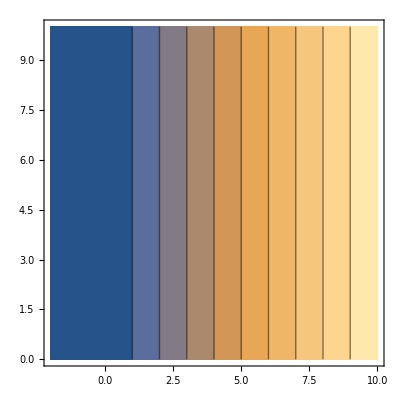

```mathematica
ContourPlot[domeval[[3]],{δ,-2,10},{ψ,0,10}]
```

```mathematica
ContourPlot[selgrad[[3]]/.{bmax->50,c->1,d->50,F[G1]->1},{δ,-2,10},{ψ,0,10}]
```

-Graphics-

```mathematica
ContourPlot[selgrad[[2]]/.{bmax->50,c->1,d->50,F[G1]->1},{δ,-2,10},{ψ,0,10}]
```

-Graphics-